```mathematica
Guy F. Mongelli                                                                                       ECHE 475
Prof. Mann                                                                                                 12/5/2012
```

```mathematica
Final Take Home Exam
```

```mathematica
Manipulate Calls of Interest: Diffusion Pulse
```

```mathematica
Problem #1:
```

```mathematica
The right handed and left handed derivatives come from the definition of a derivative (involving the limit).  The left-hand derivative is based upon the left-hand limit and the right-hand derivative on the right-hand limit.  As follows:
```

```mathematica
SubMinus[f'][x_]=Underscript[Limit, h->SuperMinus[Subscript[x, 0]]](f[x+h]-f[h])/h
```

```mathematica
SubPlus[f'][x]=Underscript[Limit, h->SuperPlus[Subscript[x, 0]]](f[x+h]-f[h])/h
```

```mathematica
f[t_]=Subscript[R, 0]*Exp[-q^2*d*Abs[t]]
```

ⅇ^(-d q^2 Abs[t]) R_0

```mathematica
D[f[t],t]
```

-d ⅇ^(-d q^2 Abs[t]) q^2 R_0 Abs'[t]

```mathematica
g[t_]=-d ⅇ^(-d q^2 Abs[t]) q^2 Subscript[R, 0] Abs'[t]
```

-d ⅇ^(-d q^2 Abs[t]) q^2 R_0 Abs'[t]

```mathematica
g[0]
```

-d q^2 R_0 Abs'[0]

```mathematica
The derivative of the absolute value function is (t/(|t|)).  Therefore, from the left we could expect a positive number and from the right, a negative number.  The slope at the t=0 point should be indeterminant since 0/0 is undefined.
```

```mathematica
For some reason Mathematica gives the left and right handed limits as zero.
```

```mathematica
Limit[(f[x+h]-f[h])/h,h->0]
```

0

```mathematica
Limit[(f[x+h]-f[h])/h,h->0,Direction->-1]
```

0

```mathematica
Limit[(f[x+h]-f[h])/h,h->0,Direction->1]
```

0

```mathematica
Part A:
```

```mathematica
Defining the autocorrelation function, Subscript[R, i][t]∝≺δC[q,t]*δC[q,0]≻.  q is the wavenumber associated with fluctuations δC[q,t].
```

```mathematica
Arbitrary constants are chosen for R0, q and d for initial plot-ability.
```

```mathematica
Subscript[R, 0]=1 ;
```

```mathematica
q=.5;
```

```mathematica
d=10^-1 (*diffusion coefficient *);
```

```mathematica
The autocorrelation function is defined:
```

```mathematica
Subscript[R, i][t_]=Subscript[R, 0]*Exp[-q^2*d*Abs[t]]
```

ⅇ^(-0.025 Abs[t])

```mathematica
Subscript[R, i][0]
```

1.

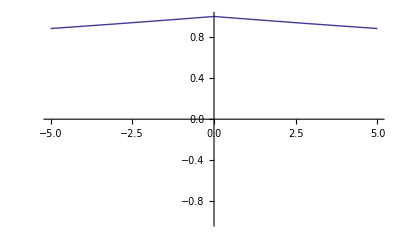

```mathematica
Plot[Subscript[R, i][t],{t,-5,5},PlotRange->{-1,1}]
```

```mathematica
D[Subscript[R, i][t],t]
```

-0.025 ⅇ^(-0.025 Abs[t]) Abs'[t]

```mathematica
D[Subscript[R, i][0]]
```

1.

```mathematica
Part B:
```

```mathematica
The spectrum function is the fourier transform of the autocorrelation function.
```

```mathematica
FourierTransform[Subscript[R, i][t],t,ω]
```

31.9154/((1.+0. ⅈ)+1600. ω^2)

```mathematica
The function is then plotted:
```

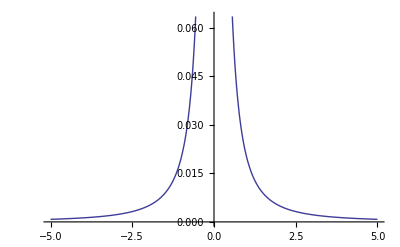

```mathematica
Plot[31.915382432114615/((1.+0. ⅈ)+1600. ω^2),{ω,-5,5}]
```

```mathematica
Clear[q,Subscript[R, 0],d]
```

Clear::ssym: R_0 is not a symbol or a string.

```mathematica
For the more general case:
```

```mathematica
FourierTransform[Subscript[R, a]*Exp[-q^2*d*Abs[t]],t,ω]
```

(d √(2/π) q^2 R_a)/(d^2 q^4+ω^2)

```mathematica
Part C:
```

```mathematica
The data set obtained Ri is known to be a function of several parameters, which are Subscript[R, 0],q^2 D,c, and |t|. c is the baseline without the noise.
```

```mathematica
σn is the uncertainty in the codomain (Ri). σt is the uncertainty of the responses in time and is negligible.
```

```mathematica
Number of data points, denoted Num, varies in each experiment.  The analysis should then include (Num+1)λ values.
```

```mathematica
Einstein equation of motion is closely related :
```

```mathematica
D=(Subscript[k, B] T)/(6πηa)
```

```mathematica
The einstein equation of motion is related to the solution of the Diffusion equation written as:
```

```mathematica
(∂ρ)/(∂t)=d(∂^2 ρ)/(∂^2 x)
```

```mathematica
with an initial condition that all particles start at the origin:
```

```mathematica
d=1;
```

```mathematica
This solution is slightly different because it is a semi-infinite domain problem but is closely relatable  to the expression given for the auto-correlation function if certain parameters are substituted for q.
```

```mathematica
ρ[x_,t_]=1/(4*Pi*d*t)^(1/2)Exp[-x^2/(4*d*t)]
```

(ⅇ^(-x^2/(4 t)))/(2 √π √t)

```mathematica
A very short time after diffusion pulse motion is started.
```

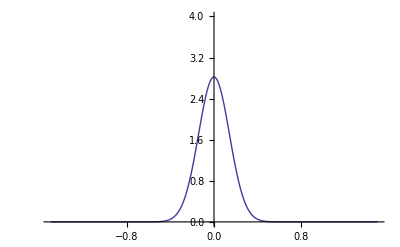

```mathematica
Plot[ρ[x,0.01],{x,-1.5,1.5},PlotRange->{0,4}]
```

```mathematica
A little bit later, the maximum concentration has decreased and the mass has moved away from the origin.  The distance
```

```mathematica
Plot[ρ[x,0.015],{x,-1.5,1.5},PlotRange->{0,4}]
```

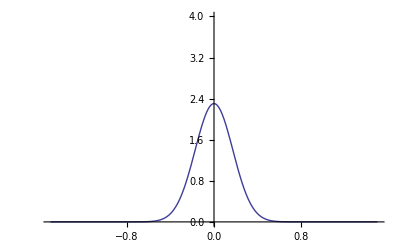

```mathematica
Manipulate[∫_-a^a ρ[x,t1]ⅆx,{a,.001,10},{t1,.001,10}]
```

```mathematica
This shows that the erf function can be generated in diffusion problems through
```

```mathematica
Int[a_]=∫_-a^a ρ[x,t1]ⅆx
```

Erf[a/(2 √t1)]

```mathematica
Manipulate[,{a,.001,10},{t1,.001,10}]
```

```mathematica
Demonstration that the diffusion function is normalized.
```

```mathematica
∫_-5^5 ρ[x,0.015]ⅆx
```

1.

```mathematica
In the following three cells the distance from the origin in x required to encompass 25% of the diffusing material is calculated.  Considering the negative axis as well, incorporates half of the initial diffusing material.
```

```mathematica
Solve[∫_0^a ρ[x,0.0015]ⅆx==.25,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→0.0369433}}

```mathematica
Solve[∫_0^a ρ[x,0.015]ⅆx==.25,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→0.116825}}

```mathematica
Solve[∫_0^a ρ[x,0.1]ⅆx==.25,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→0.301641}}

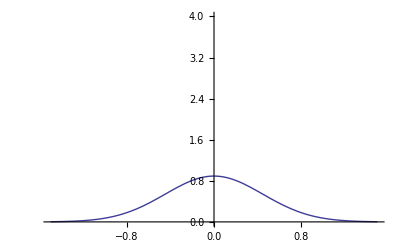

```mathematica
Plot[ρ[x,0.1],{x,-1.5,1.5},PlotRange->{0,4}]
```

```mathematica
Manipulate[Plot[ρ[x,t],{x,-1.5,1.5},PlotRange->{0,10}],{t,0.001,1.0}]
```

```mathematica
Parts of this description were inspired or obtained from Aris' text (Vectors, Tensors and the Basic Equations of Fluid Mechanics, Dover Publications Inc., 1962) as well as the online Wolfram MathWorld discussion forumns (http://mathworld.wolfram.com/NonlinearLeastSquaresFitting.html).
```

```mathematica
In order to address the uncertainties in the measured parameter, perhaps the signal as a voltage potential from a photodiode detector, one must know how many different parameters the observed value is a function of and know them to some extent over the measurement timeframe, including their uncertainties.  This number of parameters is increased by one through the addition of λ, which will be the eigenvalue(s) of the matrix that results from the non-linear least squares analysis.  This can be most easily summarized as:
```

```mathematica
Given a function f(x) of a variable x tabulated at m values, such that:
```

```mathematica
y1=f(x1)
```

```mathematica
y2=f(x2)
```

```mathematica
y3=f(x3)
```

```mathematica
...
```

```mathematica
ym=f(xm)
```

```mathematica
Assume that the function is of an analytic form depending on m parameters
 f(x;λ1,2λ,λ3,...,λn).Then consider the overdetermined (more evidence that needed to solve the system)set of equations:
```

```mathematica
y1=f(x1;λ1,λ2,λ3,...,λn)
```

```mathematica
ym=f(λ1,λ2,λ3,...,λn)
```

```mathematica
The solution of the system of equations is desired through determination of each of the λn.  This is performed readily through picking an initial guess for any value of any lambda, although λ1 seems convenient.  Then, the system is solved and if  the sum of the residuals less than a critical value ϵ (|λn|<ϵ,Einstein notation implying the sum over λn), the non-linear regression analysis is complete.  If not and the residuals are  too large, pick a different lanbda and guess again or pick the same lambda and change it's value.
```

```mathematica
Let:
```

```mathematica
ⅆ Subscript[β, i]=∑_(j=1)^n (∂f)/(∂Subscript[λ, j])*ⅆ Subscript[λ, j]|_(Subscript[x, i] λ)
```

```mathematica
for
```

```mathematica
i=1,...m
```

```mathematica
λ≡(λ1,λ2,...λn)
```

```mathematica
In component notaion, this is written:
```

```mathematica
ⅆ Subscript[β, i]=Subscript[A, ij]*ⅆ Subscript[λ, j]
```

```mathematica
In matrix form:
```

```mathematica
ⅆβ=Aⅆλ
```

```mathematica
ⅆβ is an m-vector and ⅆλ is an n-vector.  This goes back to the raising and lowering that was discussed in lecture.
```

```mathematica
The matrix, A, is then constructed:
```

```mathematica
Subscript[A, ij]=({{ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ], ..., ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ]}, {ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ], ..., ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ]}, {ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ], ⋱, ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ]}, {ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ], ..., ⅆf/(ⅆ Subscript[λ, 1])|_Subscript[x, 1λ]}})
```

```mathematica
Then apply A^T, the transpose of A, to both sides of the matrix equation:
```

```mathematica
A^T dβ=(A^T A)ⅆλ
```

```mathematica
If we let a=A^T A and b=A^T ⅆβ,then we have a matrix equation:
```

```mathematica
aⅆλ=b
```

```mathematica
The above matrix is solveable via row reduction, Gaussian elimation, LUD decomposition,matrix inversion and a wide host of techniques.
```

```mathematica
Each λ and ⅆβ can be computed.  The residuals R^2=dβ·dβ can be calculated once the minimum dλ criterian are satisfied.  That is such that the dλ correlates to a certain σn which should not be larger than that of the original data set.
```

```mathematica
To simulate this system, we can create noise artificially , with amplitude,A,and add it to the system:
```

```mathematica
A*Sin[t]
```

```mathematica
Then use the FindFit command to do the non-linear regresion on the back end.  Furthermore, programs like Excel can utilize Add-Ins like Solver to minimize the sum of the residuals under given constraints for arbitrary parameterization functional forms.  However, this method is the 'down and dirty' method.
```

```mathematica
The Error function could be sinusoidal and of an order of magnitude of σn.
```

```mathematica
Alternatively, a non-linear regression could be determined by the built-in mathematica function.
```

```mathematica
NonlinearModelFit[{Subscript[y, 1],Subscript[y, 2],…},form,{Subscript[β, 1],…},x]
```

```mathematica
data={{0,1},{1,0},{3,2},{5,4}, {6,4},{7,5}};
```

```mathematica
nlm=NonlinearModelFit[data,Log[a +b x^2],{a,b},x]
```

FittedModel[Log[1.50632+1.42633 x^2]]

```mathematica
nlm=NonlinearModelFit[data,a*Exp[b *Abs[x]],{a,b},x]
```

FittedModel[0.839871 ⅇ^(0.263312 «1»)]

```mathematica
FindFit[fp,a+b x+c Exp[x],{a,b,c},x]
```

```mathematica
The condition number of a function measures the worst case of how much a function can change with small changes in the arguement.  In the case of ill-conditioning applied to the distribution of particle sizes, in essence, there is too large of a space to be accounted for in any uncertainty.  On one hand, the data will have an error which is from the measurement problem.  On the other hand, the signal error will be more complex since it may not be clear what the distribution of particle sizes is and even if the particle size distribution is known, the signal error is likely to be on the order of magnitude of a deviation due to change in particle size.  This makes it profoundly difficult to separate between the two.  Because any error at one sized particle could be no error from another sized particle.  This introduces less certainty in the data set as a whole.
```

```mathematica
Problem 2:
```

```mathematica
Key note: The coordinate systems are defined as in Aris' definition  as opposed to my usual switched definitions in spherical coordinates.  All kinds of other information such as the Christoffel symbols for these coordinate systems are given at:
```

```mathematica
http://mathworld.wolfram.com/SphericalCoordinates.html
http://mathworld.wolfram.com/CylindricalCoordinates.html
```

```mathematica
The coordinate transformations are defined on Aris p.135 and 143:
```

```mathematica
For cylindrical to Carthesian:
```

```mathematica
x=OverTilde[x^1]=ρ*Cos[ϕ]=x^1*Cos[x^2]
```

```mathematica
y=OverTilde[x^2]=ρ*Sin[ϕ]=x^1*Sin[x^2]
```

```mathematica
z=OverTilde[x^3]=z=x^3
```

```mathematica
For carthesian to cylindrical:
```

```mathematica
ρ=OverTilde[x^1]=Sqrt[x^2+y^2]=Sqrt[(x^1)^2+(x^2)^2]
```

```mathematica
ϕ=OverTilde[x^2]=ArcTan[y/x]=ArcTan[x^2/x^1]
```

```mathematica
z=OverTilde[x^3]=z=x^3
```

```mathematica
For spherical to carthesian:
```

```mathematica
x=OverTilde[x^1]=r*Sin[θ]*Cos[ϕ]=x^1*Sin[x^2]*Cos[x^3]
```

```mathematica
y=OverTilde[x^2]=r*Sin[θ]*Sin[ϕ]=x^1*Sin[x^2]*Sin[x^3]
```

```mathematica
z=OverTilde[x^3]=r*Cos[θ]=x^1*Cos[x^2]
```

```mathematica
For carthesian to spherical:
```

```mathematica
r=OverTilde[x^1]=Sqrt[x^2+y^2+z^2]=Sqrt[(x^1)^2+(x^2)^2+(x^3)^2]
```

```mathematica
θ=OverTilde[x^2]=ArcTan[(x^2+y^2)^(1/2)]/z=ArcTan[((x^1)^2+(x^2)^2)^(1/2)]/x^3
```

```mathematica
ϕ=OverTilde[x^3]=ArcTan[y/x]=ArcTan[x^2/x^1]
```

```mathematica
Instead of using the OverTilde[x^i] convention to denote between the transormed coordinate system and the original one denoted x^i, y^i can be used for the transformed coordinate system and x^i for the original system.
```

```mathematica
The definition of the coordinate transformation gives rise to the basis which tells about the metric.  Various products of derivatives of the metric with respect to the coordinates in the transformed coordinate ststem give rise to the Christoffel symbol.  The Christoffel symbols are the interrelated to the scaling coefficients, which then give information about the legnth, surface area and volume changes that result in going from one coordinate system to another.
```

```mathematica
Although, Mathematica has the Laplacian built in, it does not have much of the Tensor mathematics that we would expect in it as a standard.  However, the Mathematica employee Eric Weisstein, who manages Mathematica Mathworld, has created a series of packages, including a tensor package.  It was originally done in Mathematica 6, some of it's functions still operate.
```

```mathematica
http://library.wolfram.com/infocenter/MathSource/4775
```

```mathematica
Phi (ϕ) is assumed to be a scalar, and grad(ϕ)=∇ϕ. The divergence of a vector field, div(ϕ)=∇·ϕ. The Laplacian is written ∇·(∇ϕ)=∇^2 ϕ.
```

```mathematica
In a tensor formulation the Laplacian is known as the Laplace–Beltrami operator.  Furthermore there is typically an absolute value of g utilized, instead of g.  However, of the basic coordinate transforms, there are none that require the absolute value due to g taking a negative value,  coordinaalthough it is not expected that g will become negative for these coordinate transforms.
```

```mathematica
∇^2 ϕ=1/g^(1/2)*∂/(∂x^i)[g^(1/2)g^ij(∂ϕ)/(∂x^i)]
```

```mathematica
∇^2 ϕ=g^ij ϕ_(,ij)
```

```mathematica
The problem statment gives the Laplacian with the covariant tensor definitions.  Additionally, consider the rectangular coordinate definition as the sum of unmixed partial derivatives.
```

```mathematica
Knowing that the Laplacian in rectangular, cylindrical and spherical coordinates are:
```

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Laplacian[f[Xx, Yy, Zz]]//Simplify
```

f^(0,0,2)[Xx,Yy,Zz]+f^(0,2,0)[Xx,Yy,Zz]+f^(2,0,0)[Xx,Yy,Zz]

```mathematica
Laplacian[f[Rr, Ttheta, Phi], Spherical]//Simplify
```

1/Rr^2(Cot[Ttheta] f^(0,1,0)[Rr,Ttheta,Phi]+f^(0,2,0)[Rr,Ttheta,Phi]+2 Rr f^(1,0,0)[Rr,Ttheta,Phi]+Rr^2 f^(2,0,0)[Rr,Ttheta,Phi])

```mathematica
Laplacian[f[Rr, Ttheta, Zz], Cylindrical]//Simplify
```

f^(0,0,2)[Rr,Ttheta,Zz]+(f^(0,2,0)[Rr,Ttheta,Zz])/Rr^2+(f^(1,0,0)[Rr,Ttheta,Zz])/Rr+f^(2,0,0)[Rr,Ttheta,Zz]

```mathematica
Other interesting functions include the Biharmonic: ∇^4 f
```

```mathematica
Part A:
```

```mathematica
The covariant derivative can be evaluated by considering the Christoffel symbols of the second kind.  They are assumed as a starting point as described based upon p. 165.  They will also be useful for Parts B and C.
```

```mathematica
The expansion of g^ij ϕ_(,ij) can be performed simply by summing the terms on the right hand side of the first expression.  First each hij is calculated, then (g^(1/2)).  But that is purpose of the next two parts of this question.  The covariant derivative is then written (Einstein notation implied):
```

```mathematica
∇^2 ϕ=∂/(∂x^i)(g^ij(∂ϕ)/(∂x^i))+({{□, i, □}, {j, □, k}})g^ik(∂ϕ)/(∂x^i)
```

```mathematica
Swapping dummy indeces i and j, and commencing index gymnastics:
```

```mathematica
({{□, i, □}, {j, □, k}})g^ik(∂ϕ)/(∂x^i)=1/g^(1/2)(∂g^(1/2))/(∂x^k)g^ik=1/g^(1/2)(∂g^(1/2))/(∂x^j)g^ij
```

```mathematica
Subtution into the line prior:
```

```mathematica
∇^2 ϕ=∂/(∂x^i)(g^ij(∂ϕ)/(∂x^i))+1/g^(1/2)(∂g^(1/2))/(∂x^j)g^ij
```

```mathematica
This is equivalent via combination of terms (product rule):
```

```mathematica
∇^2 ϕ=1/g^(1/2)∂/(∂x^j)(g^ij g^(1/2)(∂ϕ)/(∂x^i))
```

```mathematica
Part B:
```

```mathematica
The Laplacian is discussed on Aris p. 54, 169-70, and 222.  The divergence is discussed on p. 170.  The Laplacian can  be computed with Christoffel symbols or the scaling factors as 165-170 of Aris.  The information related to this problem was discussed in the notes  on 11/8/2012.
```

```mathematica
For the case of spherical coordinates the metric tensor  and dV for ∇^2 ϕ are evaluated.
```

```mathematica
The gradient of a scalar field is written as:
```

```mathematica
∇ϕ=Subscript[e, 1]/Subscript[h, 1](∂ϕ)/(∂q^1)+Subscript[e, 2]/Subscript[h, 2](∂ϕ)/dq^2+Subscript[e, 3]/Subscript[h, 3](∂ϕ)/dq^3
```

```mathematica
where h1, h2 and h3 are the [scaling constants].
```

```mathematica
The divergence of a vector field is written as:
```

```mathematica
∇·F=(1/(Subscript[h, 1] Subscript[h, 2] Subscript[h, 3]))[∂/(∂q^1)(Subscript[F, 1] Subscript[h, 2] Subscript[h, 3])+∂/dq^2(Subscript[F, 2] Subscript[h, 1] Subscript[h, 3])+∂/dq^3(Subscript[F, 3] Subscript[h, 1] Subscript[h, 2])]
```

```mathematica
The Laplacian of a scalar field is written as, and can be derived by substituting the output of the gradient into the divergence operator:
```

```mathematica
∇^2 (ϕ)=(1/(Subscript[h, 1] Subscript[h, 2] Subscript[h, 3]))[∂/(∂q^1)(Subscript[F, 1] (Subscript[h, 2] Subscript[h, 3])/Subscript[h, 1](∂ϕ)/(∂q^1))+∂/dq^2(Subscript[F, 2] (Subscript[h, 1] Subscript[h, 3])/Subscript[h, 2](∂ϕ)/(∂q^2))+∂/dq^3(Subscript[F, 3] (Subscript[h, 1] Subscript[h, 2])/Subscript[h, 3](∂ϕ)/(∂q^3))]
```

```mathematica
The scale factors Subscript[h, 1],Subscript[h, 2],Subscript[h, 3] are given for spherical and cylindrical coordinates on p. 143 of Aris.
```

```mathematica
For spherical coordinates:
```

```mathematica
Subscript[h, 1S]=1
```

1

```mathematica
Subscript[h, 2S]=(x^1)^2
```

x^2

```mathematica
Subscript[h, 3S]=(x^1 Sin[x^2])^2
```

x^2 Sin[x^2]^2

```mathematica
For cylindrical coordinates:
```

```mathematica
Subscript[h, 1C]=1
```

1

```mathematica
Subscript[h, 2C]=(x^1)^2
```

x^2

```mathematica
Subscript[h, 3C]=1
```

1

```mathematica
Substituting these coefficients into the relative positions in the metric tensor, knowing that Subscript[g, ij]=Subscript[h, ij]^2:
```

```mathematica
Subscript[g, 1S]=Subscript[h, 1S]^2
```

1

```mathematica
Subscript[g, 2S]=Subscript[h, 2S]^2
```

x^4

```mathematica
Subscript[g, 3S]=Subscript[h, 3S]^2
```

x^4 Sin[x^2]^4

```mathematica
For cylindrical coordinates:
```

```mathematica
Subscript[g, 1C]=Subscript[h, 1C]^2
```

1

```mathematica
Subscript[g, 2C]=Subscript[h, 2C]^2
```

x^4

```mathematica
Subscript[g, 3C]=Subscript[h, 3C]^2
```

1

```mathematica
For cylindrical:
```

```mathematica
(1/(Subscript[h, 1C] Subscript[h, 2C] Subscript[h, 3C]))[∂/(∂q^1)(Subscript[F, 1C] Subscript[h, 2C] Subscript[h, 3C])+∂/dq^2(Subscript[F, 2] Subscript[h, 1C] Subscript[h, 3C])+∂/dq^3(Subscript[F, 3] Subscript[h, 1C] Subscript[h, 2C])]
```

```mathematica
(1/((x^1)^2))[∂/(∂q^1)(Subscript[F, 1C] (x^1)^2)+∂/dq^2(Subscript[F, 2])+∂/dq^3(Subscript[F, 3] (x^1)^2)]
```

```mathematica
Relating back to a more familiar coordinate system:
```

```mathematica
(1/ρ)[∂/(∂ρ)((∂ϕ)/(∂ρ) ρ)+1/ρ∂^2/(d^2 ϕ)(ϕ)+ρ∂^2/(d^2 z)(ϕ)]
```

```mathematica
For spherical:
```

```mathematica
(1/(Subscript[h, 1C] Subscript[h, 2C] Subscript[h, 3C]))[∂/(∂q^1)(Subscript[F, 1] Subscript[h, 2C] Subscript[h, 3C])+∂/dq^2(Subscript[F, 2] Subscript[h, 1C] Subscript[h, 3C])+∂/dq^3(Subscript[F, 3] Subscript[h, 1C] Subscript[h, 2C])]
```

```mathematica
(1/(r^2 Sin[θ]))[Sin[θ]∂/(∂r)((∂ϕ)/(∂r) r^2)+∂^2/(d^2 θ)(Sin[θ](∂ϕ)/(∂θ))+1/Sin[θ]∂^2/(d^2 ϕ)(ϕ)]
```

```mathematica
This allows for the computation of the gradient in cylindrical coordinates(keeping in mind the difference between the scalar function ϕ and the ϕ ordinate...possibly rewrite in terms of component notation of ζ,x, and y):
```

```mathematica
∇ϕ=(∂f)/(∂ρ)Subscript[e, ρ]+1/ρ(∂ϕ)/(∂ϕ)Subscript[e, ϕ]+(∂ϕ)/(∂z)Subscript[e, z]
```

```mathematica
Each of these e is the unit vectors in that coordinate.
```

```mathematica
The gradient in spherical coordinates is:
```

```mathematica
∇ϕ=(∂f)/(∂r)Subscript[e, r]+1/r(∂ϕ)/(∂θ)Subscript[e, θ]+1/(r Sin[θ])(∂ϕ)/(∂ϕ)Subscript[e, ϕ]
```

```mathematica
The gradient in arbitrarily defined coordinates without predefined scale factors will necessitate the use of the Christoffel symbols (which are defined on Aris p. 165).
```

```mathematica
The metric tensor is computed by the equation on page 142 of Aris:
```

```mathematica
gij=∑_(k=1)^3 ((∂y^k)/(∂x^i))((∂y^k)/(∂x^j))
```

```mathematica
Each of the derivatives that appears here is computed on p. 158 for the coordinate systems of interest.
```

```mathematica
Computation of each eij fills up the metric tensor g.  The determinant of g will give insight into the volume element dV=ds3 (via a square root relationship).
```

```mathematica
As expected,the metric tensor is symmetric and the non-diagonal elements are all zero.
```

```mathematica
gS=({{1, 0, 0}, {0, r^2, 0}, {0, 0, r^2(Sin^2)[θ]}})
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin^2[θ]}}

```mathematica
Keep in mind that the determinant of the metric tensor is the same as the square root of the jacobian which comes from the transofmration matrix.
```

```mathematica
Det[gS]
```

r^4 Sin^2[θ]

```mathematica
Sqrt[Det[gS]]
```

√(r^4 Sin^2[θ])

```mathematica
This is:
```

```mathematica
r^2 Sin[θ]
```

```mathematica
dV=√g dx^1∧...∧dx^n
```

```mathematica
This is actually calculated to satisfy part C.
```

```mathematica
dVC=r^2 Sin[θ]dr dθ dϕ
```

```mathematica
gC=({{1, 0, 0}, {0, r^2, 0}, {0, 0, 1}})
```

{{1,0,0},{0,r^2,0},{0,0,1}}

```mathematica
Det[gC]
```

r^2

```mathematica
Sqrt[Det[gC]]
```

√(r^2)

```mathematica
This is:
```

```mathematica
r
```

```mathematica
dV=√g dx^1∧...∧dx^n
```

```mathematica
dVC=r dr dθ dz
```

```mathematica
Part C: For the case of cylindrical divergence utilize the metric tensor and dV for ∇·ν^(->)=ν^i are calculated as:
```

```mathematica
div(ϕ)=∇·ϕ=A_(,i)^i=g^ij Subscript[A, i,j]
```

```mathematica
where Ai is a contravariant .
```

```mathematica
In the following, ρ=r.
```

```mathematica
(1/ρ)[∂/(∂ρ)(Subscript[ϕ, ρ] ρ)+1/ρ∂^2/(d^2 ϕ)(Subscript[ϕ, ϕ])+ρ∂^2/(d^2 z)(Subscript[ϕ, z])]
```

```mathematica
Consider that these derivations were made in lecture on 10/18/2012:
```

```mathematica
A possible method to calculate the metric within Mathematica:
```

```mathematica
g[i_,j_]:=∑_(i=1)^3 (D[y[k],x[i]])*(D[y[k],x[j]])
```

```mathematica
Problem 3:
```

```mathematica
http://www.engin.umich.edu/class/bme456/ch3strain/bme456straindef.htm
```

```mathematica
http://www.doitpoms.ac.uk/tlplib/metal-forming-1/stress_tensor.php
```

```mathematica
Part A:  This equation gives the deformation of a system with respect to a reference state.
```

```mathematica
To derive the strain tensor, think of the definition of strain in the problem statement:
```

```mathematica
u^i(ξ_~,t)=x^i(ξ,t)-ξ^i
```

```mathematica
Substituting in the definition of x_~(ξ,t)=x^i(ξ_~,t)=(I_=+(A_=)_p^i(t))·ξ_=
```

```mathematica
u^i(ξ_~,t)=x^i(ξ,t)-ξ^i=x^i(ξ_~,t)=(I_=+(A_=)_p^i(t))·ξ_=-I_=ξ^i
```

```mathematica
u^i(ξ_~,t)=(A_=)_p^i(t)ξ_=
```

```mathematica
The discussion on stress tensors occurs in Aris p.88-89 and  99-105.  The relevant lectures occured on 11/8, 11/13,11/15,and 11/20.
```

```mathematica
The deformation vector u is affine, which is to say that it is a linear stransformation.  This is also known as a homogenous transformation. A key test for an affine transformation is that the midpoint of segments in the initial and final transformations are the same.
```

```mathematica
The strain tensor tells how each of the points within the region of interest undergoes a change in position that is due to the deformation tensor or the rate of strain tensor (this is motion that does not just result in the system moving). The rate of strain tensor is denoted Subscript[e, ij].  The metric can also be written in terms of the basis vectors, Subscript[ẽ, ij].
```

```mathematica
According to Aris p. 89, eq. 4.42.1 the distance between two points is:
```

```mathematica
ⅆ s^2=ⅆ Subscript[x, i]ⅆ Subscript[x, j]=((∂Subscript[x, i])/(∂Subscript[ξ, j]))((∂Subscript[x, i])/(∂Subscript[ξ, k]))ⅆ Subscript[ξ, i]ⅆ Subscript[ξ, j]=Subscript[g, ij] ⅆ Subscript[ξ, i]ⅆ Subscript[ξ, j]
```

```mathematica
We may view the deformation as simply a change of coordinate system of a non-transforming shape. Let the transformation from a coordinate system,a, into a coordinate system x-and its inverse be denoted by:
```

```mathematica
Subscript[x, i]=Subscript[x, i](Subscript[a, 1],Subscript[a, 2],Subscript[a, 3])=Subscript[ξ, i](Subscript[x, 1],Subscript[x, 2],Subscript[x, 3])
```

```mathematica
Subscript[a, i]=Subscript[a, i](Subscript[x, 1],Subscript[x, 2],Subscript[x, 3])=Subscript[x, i](Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3])
```

```mathematica
Then:
```

```mathematica
ⅆ Subscript[s, 0]^2=ⅆ Subscript[x, i]ⅆ Subscript[x, j]=((∂Subscript[x, i])/(∂Subscript[ξ, j]))((∂Subscript[x, i])/(∂Subscript[ξ, k]))ⅆ Subscript[ξ, i]ⅆ Subscript[ξ, j]=Subscript[g, ij] ⅆ Subscript[ξ, i]ⅆ Subscript[ξ, j]=Subscript[δ, kl]((∂Subscript[a, k])/(∂Subscript[x, i]))((∂Subscript[a, l])/(∂Subscript[x, j]))ⅆ Subscript[x, i]ⅆ Subscript[x, j]
```

```mathematica
ⅆ s^2=dx^2 dy^2 dz^2=d(x_~)^t UnderBar[I̲] d x_~=Subscript[δ, ij]((∂Subscript[x, i])/(∂Subscript[a, k]))((∂Subscript[x, j])/(∂Subscript[a, l]))ⅆ Subscript[a, k]ⅆ Subscript[a, l]
```

```mathematica
ⅆ s^2=(Subscript[dx, 1],Subscript[dx, 2],...,Subscript[dx, n])({{1, 0, ..., 0}, {0, 1, ..., 0}, {0, 0, ⋱, 0}, {0, ..., 0, 1}})({{Subscript[dx, 1]}, {Subscript[dx, 2]}, {...}, {Subscript[dx, n]}})
```

```mathematica
ⅆ Subscript[s, 0]^2-ⅆ s^2=(Subscript[δ, ij]((∂Subscript[x, i])/(∂Subscript[a, k]))((∂Subscript[x, j])/(∂Subscript[a, l]))-Subscript[δ, kl])ⅆ Subscript[a, k]ⅆ Subscript[a, l]=(Subscript[δ, ij]-Subscript[δ, kl]((∂Subscript[a, k])/(∂Subscript[x, i]))((∂Subscript[a, l])/(∂Subscript[x, j])))ⅆ Subscript[x, i]ⅆ Subscript[x, j]
```

```mathematica
For more interesting derivations regarding strain tensors:
```

```mathematica
http://people.ee.ethz.ch/~luethim/pdf/script/pdg/chapter4.pdf
```

```mathematica
The middle equation above is known as the Green-St. Cenant variant(Subscript[E, kl]) and the one to the right is the Cauchy variant which is discussed in Aris.  The Green's strain tensor is also known as the Lagrangian.
```

```mathematica
Subscript[E, kl]=1/2(Subscript[δ, ij]((∂Subscript[x, i])/(∂Subscript[a, k]))((∂Subscript[x, j])/(∂Subscript[a, l]))-Subscript[δ, kl])
```

```mathematica
Subscript[e, ij]=1/2(Subscript[δ, ij]-Subscript[δ, kl]((∂Subscript[a, k])/(∂Subscript[x, i]))((∂Subscript[a, l])/(∂Subscript[x, j])))
```

```mathematica
Switching dummy indices:
```

```mathematica
ⅆ Subscript[s, 0]^2-ⅆ s^2=2 Subscript[E, ij] ⅆ Subscript[a, i]ⅆ Subscript[a, j]=2 Subscript[e, ij] ⅆ Subscript[x, i]ⅆ Subscript[x, j]
```

```mathematica
The matrix above is the matric of the rectilinear coordinate system. By definition, the metric of the strain tensor is half that of the coordinate system .  This is because of the relationship between the stress tensor and the coordinate system and the way that the rate of strain tensor is defined with respect to the coordinate system.
```

```mathematica
({{Subscript[ϵ, 11], Subscript[ϵ, 12], Subscript[ϵ, 13]}, {Subscript[ϵ, 21], Subscript[ϵ, 22], Subscript[ϵ, 23]}, {Subscript[ϵ, 31], Subscript[ϵ, 32], Subscript[ϵ, 33]}})=({{1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 1])), 1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 1])), 1/2((∂Subscript[u, 1])/(∂Subscript[x, 3])+(∂Subscript[u, 3])/(∂Subscript[x, 1]))}, {1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 2])), 1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 2])), 1/2((∂Subscript[u, 2])/(∂Subscript[x, 3])+(∂Subscript[u, 3])/(∂Subscript[x, 2]))}, {1/2((∂Subscript[u, 3])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 3])), 1/2((∂Subscript[u, 3])/(∂Subscript[x, 2])+(∂Subscript[u, 2])/(∂Subscript[x, 3])), 1/2((∂Subscript[u, 3])/(∂Subscript[x, 3])+(∂Subscript[u, 3])/(∂Subscript[x, 3]))}})=({{((∂Subscript[u, 1])/(∂Subscript[x, 1])), 1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 1])), 1/2((∂Subscript[u, 1])/(∂Subscript[x, 3])+(∂Subscript[u, 3])/(∂Subscript[x, 1]))}, {1/2((∂Subscript[u, 1])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 2])), ((∂Subscript[u, 1])/(∂Subscript[x, 2])), 1/2((∂Subscript[u, 2])/(∂Subscript[x, 3])+(∂Subscript[u, 3])/(∂Subscript[x, 2]))}, {1/2((∂Subscript[u, 3])/(∂Subscript[x, 1])+(∂Subscript[u, 1])/(∂Subscript[x, 3])), 1/2((∂Subscript[u, 3])/(∂Subscript[x, 2])+(∂Subscript[u, 2])/(∂Subscript[x, 3])), ((∂Subscript[u, 3])/(∂Subscript[x, 3]))}})
```

```mathematica
such that:
```

```mathematica
(ds)^2-(ds')^2=ⅆ Subscript[x, i]ⅆ Subscript[x, i]-ⅆSubscript[x, i]'ⅆSubscript[x, i]'=2ⅆ Subscript[x, i] Subscript[u, ij] ⅆ Subscript[x, j]
```

```mathematica
Image from:
```

```mathematica
http://en.wikipedia.org/wiki/Infinitesimal_strain_theory#Strain_deviator_tensor
```

```mathematica
Considering the distance between two points as a function of time with respect to an initial reference state at t=0(p.187):
```

```mathematica
ⅆ s^2-ⅆ Subscript[s, 0]^2=Subscript[γ, ij](ξ,t)ⅆ ξ^i ⅆ ξ^j
```

```mathematica
ⅆ s^2-ⅆ Subscript[s, 0]^2=2*Subscript[γ, ij](ξ,t,t0)ⅆ ξ^i ⅆ ξ^j
```

```mathematica
where Subscript[γ, ij](ξ,t,t0)=(1/2)(Subscript[γ, ij](ξ,t)-Subscript[γ, ij](ξ,t0))
```

```mathematica
Then:
```

```mathematica
ⅆ s^2-ⅆ Subscript[s, 0]^2=2 Subscript[u, ij](ξ,t)ⅆ ξ^i ⅆ ξ^j
```

```mathematica
Part B:
```

```mathematica
The notion of second order logis refers to the fact that the considerations required are beyond first order logic (variables only range over specific sets of individuals). In this case, the considerations cannot be asserted without knowledge of tensors and curvilinear coordinates (vs. matrices).
```

```mathematica
The statement that ⅆΣ-ⅆ Subscript[Σ, 0]=Tr(u)ⅆ Subscript[Σ, 0] is simply stating that any changes in the surface area of the deforming body are purely related to (proportional to)the deformation that is ocurring along the major/principal axes of whichever coordinate system you are in.
```

```mathematica
By considering the definition of 1D rate of strain as:
```

```mathematica
ϵ̇=ⅆϵ/ⅆt=ⅆ/ⅆt((l-Subscript[l, 0])/Subscript[l, 0])
```

```mathematica
where ϵ̇ is the rate of strain,ϵ is the strain,l is the legnth in a direction, and Subscript[l, 0] is the initial legnth in a given direction.  This equation can be rearranged to a tensoral equivalent.
```

```mathematica
ⅆΣ-ⅆ Subscript[Σ, 0]=Tr(u)ⅆ Subscript[Σ, 0]
```

```mathematica
(ⅆΣ-ⅆ Subscript[Σ, 0])/(ⅆ Subscript[Σ, 0])=Tr(u)
```

```mathematica
ⅆ/(ⅆ Subscript[Σ, 0])(Σ-Subscript[Σ, 0] )=Tr(u)
```

```mathematica
That is to say that the change in surface area over the niitial surface area will be equal to the trace of u, which describes the relative expansive of shinking dilation that is occuring in the system.
```

```mathematica
An alternative method will look at how the deformations in each coordinate system accumulate into the change in surface area simmilar to the exercise in Part A.  The result is the same.
```

```mathematica
For completion, here is the definition of the wedge operator:
```

```mathematica
v=({{a}, {b}})=a*e1+b*e2,w=({{c}, {d}})=c*e1+d*e2
```

```mathematica
v∧w=(ad-bc)Subscript[e, 1]∧Subscript[e, 2]
```

```mathematica
Area=Abs[det[v w]]
```

```mathematica
Part C:
```

```mathematica
Consider for a moment an arbitrary strain tensor given by:
```

```mathematica
u=({{ϵ11, ϵ12, ϵ13}, {ϵ21, ϵ22, ϵ23}, {ϵ31, ϵ32, ϵ33}})
```

```mathematica
Please note that
```

```mathematica
The strain tensor,u, can be decomposed into a hyydrostatic/dialational part that can only change the volume of the material.  This is represented as,ud:
```

```mathematica
ud=({{ϵH, 0, 0}, {0, ϵH, 0}, {0, 0, ϵH}})
```

```mathematica
Whereas the deviatoric/pure deformations are represented as:
```

```mathematica
us=({{ϵ11-ϵH, ϵ12, ϵ13}, {ϵ21, ϵ22-ϵH, ϵ23}, {ϵ31, ϵ32, ϵ33-ϵH}})
```

```mathematica
The hydrostatic stress should be 1/3 the sum of the principal strains (σ1+σ2+σ3)-which are relateable to principal stresses.  This is 1/3 of the trace of u.
```

```mathematica
ϵH=(1/3)(ϵ1+ϵ2+ϵ3) (* ϵ11=ϵ1,σ22=ϵ2,σ33=ϵ3? *)
```

```mathematica
ϵIn the context of showing that u_==u_(↔s)+u_(↔d)
```

```mathematica
where:
```

```mathematica
u_(↔s)= u_=-1/2 Tr(u_=)δ_=
```

```mathematica
u_(↔d)= u_=-1/2 Tr(u_=)δ_=
```

```mathematica
Since the Tr(u_=) is fixed by the deformation process, as are Subscript[u, S] and Subscript[u, d] are also fixed.  Since Subscript[u, d] is a row reduced and diagonalized form of u, and Subscript[u, s] is u-Subscript[u, d].  Therefore δ must indicate something about the relative contributions of the dialational and shearing properties of u.  The obvious difference being that one differential is in space and the other is in time.  This is due to the change in conceptualization between deformation and chnging coordinate systems but the coceptualization.
```

```mathematica
δ tells us about what is happening to the strain tensor during the diagnalization process.
```

```mathematica
Part D:  In order to construct the Subscript[A, p]^i(t) tensor for purely dialational deformation, it is best to start with the purely dialational deformation as it pertains to the strain equation and then work back to Subscript[A, p]^i(t).
```

```mathematica
Let
```

```mathematica
u=ud=({{ϵH, 0, 0}, {0, ϵH, 0}, {0, 0, ϵH}})
```

```mathematica
There is an integration to solve a matrix equation that related the rate of strain to the position change
```

```mathematica
u=d/dt(A(t))
```

```mathematica
A is not a function of time and is filled with constants.  Solving each equation independently, since they are unrelated/uncoupled.  The boundary conditions are that at t=0 there is not strain on the system and at t=tf, there is a certain strain on the system that resulted from a rate of deformation.
```

```mathematica
A=u=ud*t=({{σϵ*t/tf, 0, 0}, {0, σϵ*t/tf, 0}, {0, 0, σϵ*t/tf}})
```

```mathematica
where the final strains occur at time tf and the strain occurst constantly.Although, one could imagine a myriad of different eqivalent, non-constant strains that result in the eqivalent final deformation.  There is a hint of caution here since there are many stresses and strains that can impart irreversible changes in the material propertie s of the system (fracture).
```

```mathematica
Apart from direct measurement of deformations in various physical axes under simplest comditions such as a 1D strain.Ultrasound as been used to measure the strain tensor of arterial walls: http://iopscience.iop.org/0031-9155/55/21/003.
```

```mathematica
Any other techniques that can record 3D shape information and then perform downstream computations on it could theoretically calculate such an affine strain tensor.  Examples are MRI scans,PT scans, and simple camera images (Google has the ability to constrict 3D models of a system through taking many pictures of a system).
```

```mathematica
Problem 4:
```

```mathematica
Part A:
```

```mathematica
∇·[ϵ(r)*∇Φ(r)]=0
```

```mathematica
The gradient, as seen in Problem 2, will take a scalar and take the covariant derivative , lowering an undex.  Then the result is multiplied by epsilon of r and the divergance is taken which will lower the index.  Therefore the left hand side should be t_□^□11 and the right hand side is (Subscript[t, 0]^0).
```

```mathematica
Therefore this equations is inconsistent.  The equation should include the metric tensor or it's conjugate to raise and lower indeces appropriately such that the equation is tensorially correct.
```

```mathematica
The same problem exists in the second equation.  This is because ϵ(r) is a scalar(Subscript[t, 0]^0) and n is a scalar(Subscript[t, 0]^0), and the remaining terms are mixed.  Again, wherever the gradient operator (covariant) is present, the metric (contravariant) tensor should be present to raise an index and make the equation consistent.  The denominator of the second term in parenthese picks up two factors of ∇ψ and the first one picks up only one.  The cosh of a scalar is a scalar. and yet it is divided by a vector.  Therefore there are two vector terms present and subtracting them does not alleviate this issue.
```

```mathematica
Regarding the phenomena governed by the equations, it appears that the electric field and the dielectric constant are both functions of r because they are interacting.  For NL optical systems, the dielectric constant and therefore the electric field propagation though the system can interact based upon the stregnth of the electric field.  The cyclical cause and effect (chicken and egg) relationship is very common in optics.
```

```mathematica
ϵ(r)=n^2+((3(ϵ^0-n^2))/(β∇Φ(r)))[Coth[∇Φ(r)]-1/(β∇Φ(r))]
```

```mathematica
FullSimplify[D[n^2+((3(ϵ^0-n^2))/(β∇Φ(r)))[Coth[∇Φ(r)]-1/(β∇Φ(r))],r]]
```

(3 (-1+n^2))/(r^2 β ∇Φ)[Coth[r ∇Φ]-1/(r β ∇Φ)]+(1/(r^2 β ∇Φ)-Csch[r ∇Φ]^2 ∇Φ) ((3-3 n^2)/(r β ∇Φ))'[Coth[r ∇Φ]-1/(r β ∇Φ)]

```mathematica
FullSimplify[D[D[n^2+((3(ϵ^0-n^2))/(β∇Φ(r)))[Coth[∇Φ(r)]-1/(β∇Φ(r))],r],r]]
```

```mathematica
((6-6 n^2)/(r^3 β ∇Φ))[Coth[r ∇Φ]-1/(r β ∇Φ)]+(1/(r^2 β ∇Φ)-Csch[r ∇Φ]^2 ∇Φ) (((3 (-1+n^2))/(r^2 β ∇Φ))')[Coth[r ∇Φ]-1/(r β ∇Φ)]+(-2/(r^3 β ∇Φ)+2 Coth[r ∇Φ] Csch[r ∇Φ]^2 (∇Φ)^2) (((3-3 n^2)/(r β ∇Φ))')[Coth[r ∇Φ]-1/(r β ∇Φ)]+(1/(r^2 β ∇Φ)-Csch[r ∇Φ]^2 ∇Φ) ((1/(r^2 β ∇Φ)-Csch[r ∇Φ]^2 ∇Φ) (((3-3 n^2)/(r β ∇Φ))'')[Coth[r ∇Φ]-1/(r β ∇Φ)]+((3 (-1+n^2) ((3-3 n^2)/(r β ∇Φ))'')/(r^2 β ∇Φ))[Coth[r ∇Φ]-1/(r β ∇Φ)])
```

```mathematica
The information on gradients is presented on p.51 of Aris.
```

```mathematica
When I was attempting to determine how you rearranged to get the dielectric constant from eq 2.8 in Boothe, I actually referred to the relationship between dielectric constant and refractive index from my master's thesis in Ch. 3.
```

```mathematica
The key to deriving the shown equation s is described here.  The first equation is one of Maxwell's equations ,Gauss' Law,for a vacuum system with no enclosed charge and no current(∇·E=0).  The electric field intensity E is substituted for ϵ(r)∇Φ(r) indicating that the electric field and therefore dielectric constant  are functions of r.  This is true in non-linear optical systems because the dielectric constant (and ϵ-dependent refractive index n) is dependent upon the applied field stregnth.  Presumably, β=kB*T.
```

```mathematica
The second equation shown is not derived directly in the test but is a substitution of Eq. 2.6 intp 2.7
```

```mathematica
, and then a substitution of the result into eq. 2,1.  Then the relation is solved for ϵ(r). x is then evaluated at β∇Φ(r).
```

```mathematica
This problem, however, is getting at the realtionship between the operations on the left and right hand side.
```

```mathematica
∇·[ϵ(r)∇Φ(r)]]=0.
```

```mathematica
The left hand side is the gradient applied to a scalar multiplied by a gradient of Φ(r).  The gradient is a 1-form which is a covariant vector, represented as (Subscript[t, 1]^0).  The divergence of a vector field is a scalar, and should be represented as  (Subscript[t, 0]^1).  These two functions are inverse operators in terms of the way they accept scalars/tensors and output tensors/scalars.  Therefore, the left hand side is a scalar (no rank in terms of contravariance or covariance).
```

```mathematica
The right hand side is a scalar (no rank in contravariance or covariance).
```

```mathematica
Part B:
```

```mathematica
Covariant tensors get lower indeces and contravariants get upper indices.
```

```mathematica
The original Langevin equation (Langevin,P.(1908)."On the Theory of Brownian Motion".C.R.Acad.Sci.(Paris) 146:530–533) is given as:
```

```mathematica
m*(d^2 x)/(d^2 t)=-λ*dx/dt+η(t)
```

```mathematica
A more general Langevin equation (Hohenberg,P.C.;Halperin,B.I.(1977)."Theory of dynamic critical phenomena".Reviews of Modern Physics 49 (3):435–479.)reads:
```

```mathematica
Subscript[dA, i]/dt=Subscript[k, B]*T∑_j [Subscript[A, i],Subscript[A, j]] dℋ/Subscript[dA, j]-∑_j Subscript[λ, i,j](A)dℋ/Subscript[dA, j]-∑_j (Subscript[dλ, i,j][A])/Subscript[dA, j]+Subscript[η, i][t]
```

```mathematica
Subscript[η, i][t] typically obeys a Gaussian probability distribution.
```

```mathematica
In order to make this out proper index notation as sene in lecture, the sumnations are dropped.
```

```mathematica
Subscript[dA, i]/dt=Subscript[k, B]*T[Subscript[A, i],Subscript[A, j]] dℋ/Subscript[dA, j]-Subscript[λ, i,j](A)dℋ/Subscript[dA, j]-(Subscript[dλ, i,j][A])/Subscript[dA, j]+Subscript[η, i][t]
```

```mathematica
[Subscript[A, i],Subscript[A, j]] represents the Poisson bracket as defined:
```

```mathematica
[f,g]=∑_(i=1)^N ((∂f)/(∂Subscript[q, i])(∂g)/(∂Subscript[p, i])-(∂f)/(∂Subscript[q, i])(∂g)/(∂Subscript[p, i]))
```

```mathematica
where f and g are functions of Subscript[p, i],Subscript[q, i],and t.
```

```mathematica
ℋ is the Hamiltonian for the system and in the case of Brownian motion is (p^2/(2m Subscript[k, B] T)).  Note the symmetry in this equation, Subscript[λ, ij]=Subscript[λ, ji].
```

```mathematica
In index free notation:
```

```mathematica
m(ⅆ u̲)/ⅆt=-ζ u̲+F(t)
```

```mathematica
m is the mass of the particle
```

```mathematica
u̲ is the instantaneous velocity tensor.
```

```mathematica
ζ=6πμR
```

```mathematica
μ=viscosity of fluid
```

```mathematica
R=particle radius
```

```mathematica
F(t)=rapidly, oscillating and irregular motion Brownian motion force (can be connected to fluctuations in Statistical mechanics)
```

```mathematica
For implementation of code to sole the Langevin equation, check http://mathematica.stackexchange.com/questions/8744/efficient-langevin-equation-solver.  This is actually intimately related to the problem of error analysis as given in the first problem part C.
```

```mathematica
This equation applies to thermal noise (Johnson noise) in an electrica resistor.  Where there are a resistor and capacitor in series with no other elements and the voltage is measured.  For small capacitance, the thermal fluctuations can become significant relative to the total voltage in the system and the hamiltonian of the system is given as H=E/(Subscript[k, B] T)=CU^2/(2 Subscript[k, B] t).
```

```mathematica
The Langevin equation has implications in the diffusion of colloidal systems, as we have seen in Brownian motion several times before in this course.  For more information, see Bird, Steward and Lightfoot p.531.
```